```mathematica
(*Початоква купа формул*)
ClearAll[x,t,L,Gtailor,G,y,u,uI,t1,t2,x1,x2,T,TI,X,XI,Gx]
L=(D[#,t]-D[#,{x,2}])&
G=(t/Sqrt[4Pi*t]*Exp[-x^2/(4t)])(*/.{t->(t-tI),x->(x-xI)}*)
aproxNormal=3(16428+15925x^2)*Exp[-39x+111ArcTan[35x/111]]/(12321+1225x^2)/(Exp[-39x+111ArcTan[35x/111]]+1)^2/.{x->x/1.77}
Gaprox=(t/Sqrt[t]*aproxNormal^(1/(4t)))/.{t->(t-tI),x->(x-xI)}
(*Gtailor=Simplify[Normal[Series[G,{x,1,2},{t,1,2}]]]/.{t->(t-tI),x->(x-xI)}*)
G=G/.{t->(t-tI),x->(x-xI)}
y:=Sin[x]*Sin[t]
u := L[y]
uI:=u/.{x->xI,t->tI}
(*Просторово-часова область*)
t1:=1
t2:=50
x1:=1
x2:=50
T:={t,t1,t2}
TI:=T/.{t->tI}
X:={x,x1,x2}
XI:=X/.{x->xI}
```

∂_t #1-∂_{x,2} #1&

(ⅇ^(-x^2/(4 t)) √t)/(2 √π)

(3 ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]) (16428+5083.15 x^2))/((1+ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]))^2 (12321+391.012 x^2))

3^(1/(4 (t-tI))) √(t-tI) ((ⅇ^(-22.0339 (x-xI)+111 ArcTan[0.178144 (x-xI)]) (16428+5083.15 (x-xI)^2))/((1+ⅇ^(-22.0339 (x-xI)+111 ArcTan[0.178144 (x-xI)]))^2 (12321+391.012 (x-xI)^2)))^(1/(4 (t-tI)))

(ⅇ^(-(x-xI)^2/(4 (t-tI))) √(t-tI))/(2 √π)

3^(1/4) ((ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]) (16428+5083.15 x^2))/((1+ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]))^2 (12321+391.012 x^2)))^(1/4)

(3 ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]) (16428+5083.15 x^2))/((1+ⅇ^(-22.0339 x+111 ArcTan[0.178144 x]))^2 (12321+391.012 x^2))

ⅇ^(-x^2)

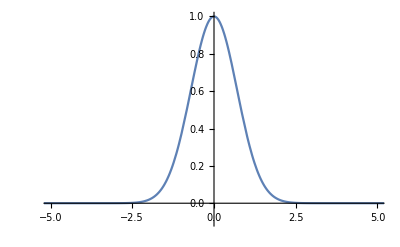

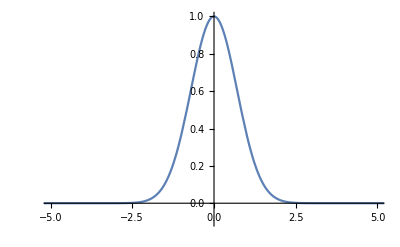

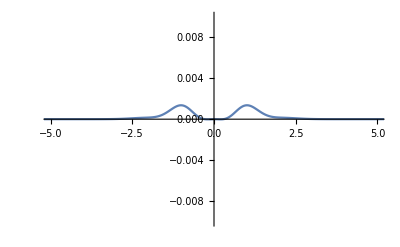

```mathematica
Gtailorx=Gaprox/.{t->1,tI->0,xI->0}
Gtailorx=3(16428+15925x^2)*Exp[-39x+111ArcTan[35x/111]]/(12321+1225x^2)/(Exp[-39x+111ArcTan[35x/111]]+1)^2/.{x->x/1.77}
Gx=Exp[-x^2]/.{t->1,tI->0,xI->0}
Plot[Gx, {x,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
Plot[Gtailorx, {x,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
Plot[Gx-Gtailorx, {x,-10,20},PlotRange->{{-5,5},{-0.01,0.01}}]
```

0.366527^(1/4/t) √t

(ⅇ^(-1/4/t) √t)/(2 √π)

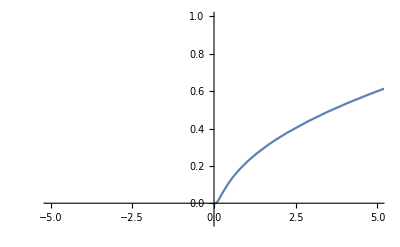

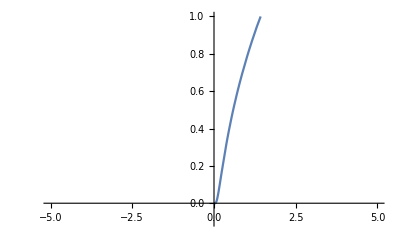

```mathematica
Gtailort=Gaprox/.{x->1,tI->0,xI->0}
Gt=G/.{x->1,tI->0,xI->0}
Plot[Gt, {t,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
Plot[Gtailort, {t,-10,20},PlotRange->{{-5,5},{-0.1,1}}]
```

```mathematica
Gaprox*uI
```

3^(1/(4 (t-tI))) √(t-tI) ((ⅇ^(-22.0339 (x-xI)+111 ArcTan[0.178144 (x-xI)]) (16428+5083.15 (x-xI)^2))/((1+ⅇ^(-22.0339 (x-xI)+111 ArcTan[0.178144 (x-xI)]))^2 (12321+391.012 (x-xI)^2)))^(1/(4 (t-tI))) (Cos[tI] Sin[xI]+Sin[tI] Sin[xI])

```mathematica
(*Перший у*)
yInf=Simplify[Integrate[Gaprox,Evaluate[XI],Evaluate[TI]]]
```

$Aborted

```mathematica
(*Точки для подбудови вектори U*)
(*m0:={{xI->1,tI->-10},{xI->2,tI->-20},{xI->3,tI->-30},{xI->4,tI->-1},{xI->5,tI->-2}}
mE:={{xI->100,tI->1},{xI->200,tI->30},{xI->55,tI->10},{xI->65,tI->20},{xI->75,tI->30}}*)
m0:={{xI->1,tI->-10},{xI->2,tI->-20}}
size0:=Length[m0]
mE:={{xI->100,tI->1},{xI->200,tI->30}}
sizeE:=Length[mE]

(* Області (початкова і гранична) *)
region0:=Boole[t==0&&x≠x2&&x≠x1]
regionE:=Boole[t!=0&&x==x2&&x==x1]
```

```mathematica
Gm0:=G/.m0
GmE:=G/.mE
```

```mathematica
(*Вектор В*)
B11:=Gm0*region0
B12:=GmE*region0
B21:=Gm0*regionE
B22:=GmE*regionE
B:={Join[B11,B12],Join[B21,B22]}
B//MatrixForm
Transpose[B]//MatrixForm
```

((ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t==0&&x≠50&&x≠1])/(2 √π)
(ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t≠0&&x==50&&x==1])/(2 √π))

((ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-1+x)^2/(4 (10+t))) √(10+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-2+x)^2/(4 (20+t))) √(20+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-100+x)^2/(4 (-1+t))) √(-1+t) Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-(-200+x)^2/(4 (-30+t))) √(-30+t) Boole[t≠0&&x==50&&x==1])/(2 √π))

```mathematica
(*Вектор У з областями*)
Y:={y*region0,y*regionE}
```

```mathematica
By=Integrate[(Transpose[B].Y)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].Y)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].Y)/.{x->x2},Evaluate[T]]
```

{0,0,0,0}

```mathematica
P=PseudoInverse[Integrate[(Transpose[B].B)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].B)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].B)/.{x->x2},Evaluate[T]]]
```

General::ovfl: Overflow occurred in computation.

```mathematica
u0=P[[1;;size0]].By
```

```mathematica
uE=P[[size0+1;;]].By
```

```mathematica
yFull=yInf+Gm0.u0+GmE.uE
yFull
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate